```mathematica
phdos=Import[NotebookDirectory[]<>"csi.phdos"];
```

```mathematica
phdos[[1]]
```

{#,Frequency[cm^-1],DOS,PDOS}

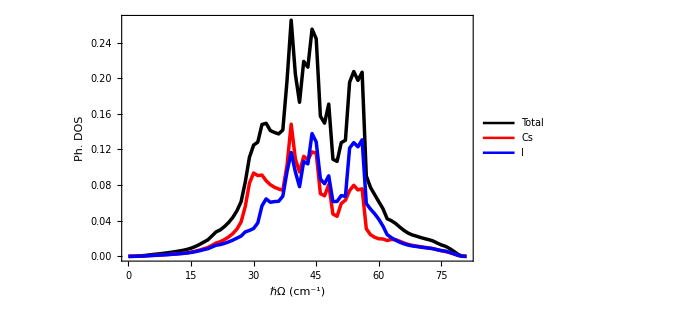

```mathematica
ListPlot[{phdos[[2;;All,{1,2}]],phdos[[2;;All,{1,3}]],phdos[[2;;All,{1,4}]]},PlotRange->All,Joined->True,InterpolationOrder->1,Frame->True,PlotStyle->{Directive[Black,Thickness[0.005]],Directive[Red,Thickness[0.005]],Directive[Blue,Thickness[0.005]]},FrameLabel->{{Style["Ph. DOS",20,Black],""},{Style["ℏΩ (cm^-1)",20,Black],""}},LabelStyle->Directive[FontSize->18,FontFamily->"Times",Black],FrameStyle->Directive[Thickness[0.002],Black],PlotLegends->{"Total","Cs","I"},ImageSize->500]
```